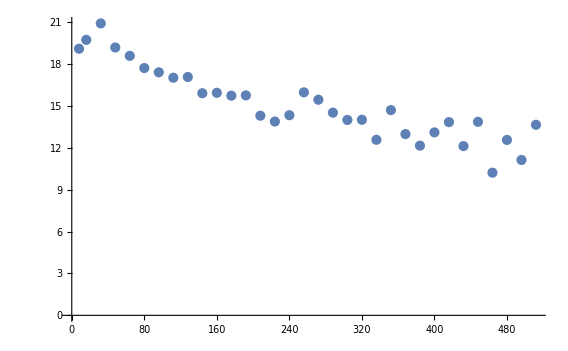

```mathematica
ListPlot[Callout[#,#]&/@({#[[1]],Log2[#[[2]]]}&/@{{8,569450},{16,884680},{32,2006191},{48,605195},{64,399429},{80,218237},{96,176408},{112,134652},{128,139622},{144,62300},{160,63658},{176,55235},{192,55954},{208,20408},{224,15249},{240,20919},{256,65133},{272,45155},{288,23740},{304,16503},{320,16656},{336,6163},{352,26964},{368,8181},{384,4599},{400,8897},{416,14815},{432,4499},{448,15035},{464,1201},{480,6117},{496,2260},{512,12996}})]
```

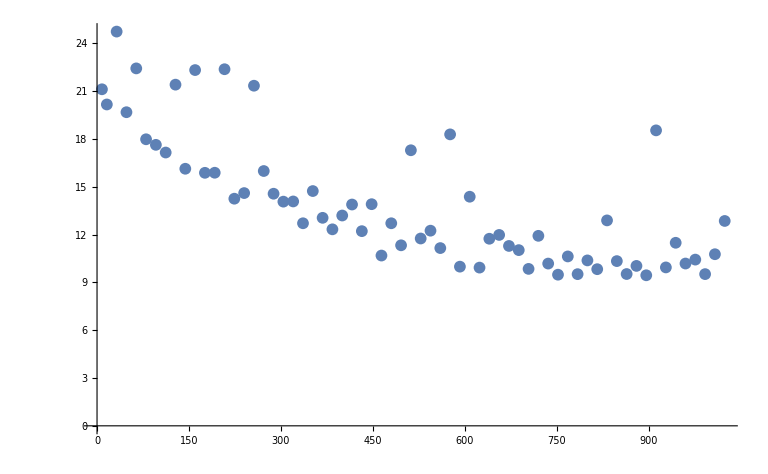

```mathematica
data={{8,2284324},{16,1179376},{32,28105445},{48,841919},{64,5667532},{80,259483},{96,203706},{112,145789},{128,2792944},{144,71964},{160,5268332},{176,60309},{192,60524},{208,5463507},{224,19562},{240,24978},{256,2667213},{272,65212},{288,24284},{304,17205},{320,17353},{336,6718},{352,27279},{368,8511},{384,5160},{400,9411},{416,15184},{432,4766},{448,15403},{464,1649},{480,6717},{496,2575},{512,160917},{528,3462},{544,4866},{560,2282},{576,321122},{592,1017},{608,21317},{624,976},{640,3425},{656,4044},{672,2504},{688,2088},{704,923},{720,3889},{736,1163},{752,717},{768,1587},{784,734},{800,1335},{816,911},{832,7610},{848,1295},{864,738},{880,1051},{896,699},{912,382329},{928,984},{944,2874},{960,1165},{976,1382},{992,735},{1008,1747},{1024,7425}};
ListPlot[Callout[#,#]&/@({#[[1]],Log2[#[[2]]]}&/@data)]
```

```mathematica
Table[(Table[{sz,cnt,NumberForm[100.(4096p-sz cnt)/(4096p),{2,1}]}/.{cnt->Floor[(4096p)/sz]}/.{sz->Max[i,8]},{p,1,8}]),{i,0,1024,16}]//MatrixForm
```

((8
512
0.0) | (8
1024
0.0) | (8
1536
0.0) | (8
2048
0.0) | (8
2560
0.0) | (8
3072
0.0) | (8
3584
0.0) | (8
4096
0.0)
(16
256
0.0) | (16
512
0.0) | (16
768
0.0) | (16
1024
0.0) | (16
1280
0.0) | (16
1536
0.0) | (16
1792
0.0) | (16
2048
0.0)
(32
128
0.0) | (32
256
0.0) | (32
384
0.0) | (32
512
0.0) | (32
640
0.0) | (32
768
0.0) | (32
896
0.0) | (32
1024
0.0)
(48
85
0.4) | (48
170
0.4) | (48
256
0.0) | (48
341
0.1) | (48
426
0.2) | (48
512
0.0) | (48
597
0.1) | (48
682
0.1)
(64
64
0.0) | (64
128
0.0) | (64
192
0.0) | (64
256
0.0) | (64
320
0.0) | (64
384
0.0) | (64
448
0.0) | (64
512
0.0)
(80
51
0.4) | (80
102
0.4) | (80
153
0.4) | (80
204
0.4) | (80
256
0.0) | (80
307
0.1) | (80
358
0.1) | (80
409
0.1)
(96
42
1.6) | (96
85
0.4) | (96
128
0.0) | (96
170
0.4) | (96
213
0.2) | (96
256
0.0) | (96
298
0.2) | (96
341
0.1)
(112
36
1.6) | (112
73
0.2) | (112
109
0.7) | (112
146
0.2) | (112
182
0.5) | (112
219
0.2) | (112
256
0.0) | (112
292
0.2)
(128
32
0.0) | (128
64
0.0) | (128
96
0.0) | (128
128
0.0) | (128
160
0.0) | (128
192
0.0) | (128
224
0.0) | (128
256
0.0)
(144
28
1.6) | (144
56
1.6) | (144
85
0.4) | (144
113
0.7) | (144
142
0.2) | (144
170
0.4) | (144
199
0.1) | (144
227
0.2)
(160
25
2.3) | (160
51
0.4) | (160
76
1.0) | (160
102
0.4) | (160
128
0.0) | (160
153
0.4) | (160
179
0.1) | (160
204
0.4)
(176
23
1.2) | (176
46
1.2) | (176
69
1.2) | (176
93
0.1) | (176
116
0.3) | (176
139
0.5) | (176
162
0.6) | (176
186
0.1)
(192
21
1.6) | (192
42
1.6) | (192
64
0.0) | (192
85
0.4) | (192
106
0.6) | (192
128
0.0) | (192
149
0.2) | (192
170
0.4)
(208
19
3.5) | (208
39
1.0) | (208
59
0.1) | (208
78
1.0) | (208
98
0.5) | (208
118
0.1) | (208
137
0.6) | (208
157
0.3)
(224
18
1.6) | (224
36
1.6) | (224
54
1.6) | (224
73
0.2) | (224
91
0.5) | (224
109
0.7) | (224
128
0.0) | (224
146
0.2)
(240
17
0.4) | (240
34
0.4) | (240
51
0.4) | (240
68
0.4) | (240
85
0.4) | (240
102
0.4) | (240
119
0.4) | (240
136
0.4)
(256
16
0.0) | (256
32
0.0) | (256
48
0.0) | (256
64
0.0) | (256
80
0.0) | (256
96
0.0) | (256
112
0.0) | (256
128
0.0)
(272
15
0.4) | (272
30
0.4) | (272
45
0.4) | (272
60
0.4) | (272
75
0.4) | (272
90
0.4) | (272
105
0.4) | (272
120
0.4)
(288
14
1.6) | (288
28
1.6) | (288
42
1.6) | (288
56
1.6) | (288
71
0.2) | (288
85
0.4) | (288
99
0.6) | (288
113
0.7)
(304
13
3.5) | (304
26
3.5) | (304
40
1.0) | (304
53
1.7) | (304
67
0.5) | (304
80
1.0) | (304
94
0.3) | (304
107
0.7)
(320
12
6.3) | (320
25
2.3) | (320
38
1.0) | (320
51
0.4) | (320
64
0.0) | (320
76
1.0) | (320
89
0.7) | (320
102
0.4)
(336
12
1.6) | (336
24
1.6) | (336
36
1.6) | (336
48
1.6) | (336
60
1.6) | (336
73
0.2) | (336
85
0.4) | (336
97
0.5)
(352
11
5.5) | (352
23
1.2) | (352
34
2.6) | (352
46
1.2) | (352
58
0.3) | (352
69
1.2) | (352
81
0.6) | (352
93
0.1)
(368
11
1.2) | (368
22
1.2) | (368
33
1.2) | (368
44
1.2) | (368
55
1.2) | (368
66
1.2) | (368
77
1.2) | (368
89
0.0)
(384
10
6.3) | (384
21
1.6) | (384
32
0.0) | (384
42
1.6) | (384
53
0.6) | (384
64
0.0) | (384
74
0.9) | (384
85
0.4)
(400
10
2.3) | (400
20
2.3) | (400
30
2.3) | (400
40
2.3) | (400
51
0.4) | (400
61
0.7) | (400
71
0.9) | (400
81
1.1)
(416
9
8.6) | (416
19
3.5) | (416
29
1.8) | (416
39
1.0) | (416
49
0.5) | (416
59
0.1) | (416
68
1.3) | (416
78
1.0)
(432
9
5.1) | (432
18
5.1) | (432
28
1.6) | (432
37
2.4) | (432
47
0.9) | (432
56
1.6) | (432
66
0.6) | (432
75
1.1)
(448
9
1.6) | (448
18
1.6) | (448
27
1.6) | (448
36
1.6) | (448
45
1.6) | (448
54
1.6) | (448
64
0.0) | (448
73
0.2)
(464
8
9.4) | (464
17
3.7) | (464
26
1.8) | (464
35
0.9) | (464
44
0.3) | (464
52
1.8) | (464
61
1.3) | (464
70
0.9)
(480
8
6.3) | (480
17
0.4) | (480
25
2.3) | (480
34
0.4) | (480
42
1.6) | (480
51
0.4) | (480
59
1.2) | (480
68
0.4)
(496
8
3.1) | (496
16
3.1) | (496
24
3.1) | (496
33
0.1) | (496
41
0.7) | (496
49
1.1) | (496
57
1.4) | (496
66
0.1)
(512
8
0.0) | (512
16
0.0) | (512
24
0.0) | (512
32
0.0) | (512
40
0.0) | (512
48
0.0) | (512
56
0.0) | (512
64
0.0)
(528
7
9.8) | (528
15
3.3) | (528
23
1.2) | (528
31
0.1) | (528
38
2.0) | (528
46
1.2) | (528
54
0.6) | (528
62
0.1)
(544
7
7.0) | (544
15
0.4) | (544
22
2.6) | (544
30
0.4) | (544
37
1.7) | (544
45
0.4) | (544
52
1.3) | (544
60
0.4)
(560
7
4.3) | (560
14
4.3) | (560
21
4.3) | (560
29
0.9) | (560
36
1.6) | (560
43
2.0) | (560
51
0.4) | (560
58
0.9)
(576
7
1.6) | (576
14
1.6) | (576
21
1.6) | (576
28
1.6) | (576
35
1.6) | (576
42
1.6) | (576
49
1.6) | (576
56
1.6)
(592
6
13.0) | (592
13
6.1) | (592
20
3.6) | (592
27
2.4) | (592
34
1.7) | (592
41
1.2) | (592
48
0.9) | (592
55
0.6)
(608
6
11.0) | (608
13
3.5) | (608
20
1.0) | (608
26
3.5) | (608
33
2.0) | (608
40
1.0) | (608
47
0.3) | (608
53
1.7)
(624
6
8.6) | (624
13
1.0) | (624
19
3.5) | (624
26
1.0) | (624
32
2.5) | (624
39
1.0) | (624
45
2.1) | (624
52
1.0)
(640
6
6.3) | (640
12
6.3) | (640
19
1.0) | (640
25
2.3) | (640
32
0.0) | (640
38
1.0) | (640
44
1.8) | (640
51
0.4)
(656
6
3.9) | (656
12
3.9) | (656
18
3.9) | (656
24
3.9) | (656
31
0.7) | (656
37
1.2) | (656
43
1.6) | (656
49
1.9)
(672
6
1.6) | (672
12
1.6) | (672
18
1.6) | (672
24
1.6) | (672
30
1.6) | (672
36
1.6) | (672
42
1.6) | (672
48
1.6)
(688
5
16.0) | (688
11
7.6) | (688
17
4.8) | (688
23
3.4) | (688
29
2.6) | (688
35
2.0) | (688
41
1.6) | (688
47
1.3)
(704
5
14.0) | (704
11
5.5) | (704
17
2.6) | (704
23
1.2) | (704
29
0.3) | (704
34
2.6) | (704
40
1.8) | (704
46
1.2)
(720
5
12.0) | (720
11
3.3) | (720
17
0.4) | (720
22
3.3) | (720
28
1.6) | (720
34
0.4) | (720
39
2.1) | (720
45
1.1)
(736
5
10.0) | (736
11
1.2) | (736
16
4.2) | (736
22
1.2) | (736
27
3.0) | (736
33
1.2) | (736
38
2.5) | (736
44
1.2)
(752
5
8.2) | (752
10
8.2) | (752
16
2.1) | (752
21
3.6) | (752
27
0.9) | (752
32
2.1) | (752
38
0.3) | (752
43
1.3)
(768
5
6.3) | (768
10
6.3) | (768
16
0.0) | (768
21
1.6) | (768
26
2.5) | (768
32
0.0) | (768
37
0.9) | (768
42
1.6)
(784
5
4.3) | (784
10
4.3) | (784
15
4.3) | (784
20
4.3) | (784
26
0.5) | (784
31
1.1) | (784
36
1.6) | (784
41
1.9)
(800
5
2.3) | (800
10
2.3) | (800
15
2.3) | (800
20
2.3) | (800
25
2.3) | (800
30
2.3) | (800
35
2.3) | (800
40
2.3)
(816
5
0.4) | (816
10
0.4) | (816
15
0.4) | (816
20
0.4) | (816
25
0.4) | (816
30
0.4) | (816
35
0.4) | (816
40
0.4)
(832
4
19.0) | (832
9
8.6) | (832
14
5.2) | (832
19
3.5) | (832
24
2.5) | (832
29
1.8) | (832
34
1.3) | (832
39
1.0)
(848
4
17.0) | (848
9
6.8) | (848
14
3.4) | (848
19
1.7) | (848
24
0.6) | (848
28
3.4) | (848
33
2.4) | (848
38
1.7)
(864
4
16.0) | (864
9
5.1) | (864
14
1.6) | (864
18
5.1) | (864
23
3.0) | (864
28
1.6) | (864
33
0.6) | (864
37
2.4)
(880
4
14.0) | (880
9
3.3) | (880
13
6.9) | (880
18
3.3) | (880
23
1.2) | (880
27
3.3) | (880
32
1.8) | (880
37
0.6)
(896
4
13.0) | (896
9
1.6) | (896
13
5.2) | (896
18
1.6) | (896
22
3.8) | (896
27
1.6) | (896
32
0.0) | (896
36
1.6)
(912
4
11.0) | (912
8
11.0) | (912
13
3.5) | (912
17
5.4) | (912
22
2.0) | (912
26
3.5) | (912
31
1.4) | (912
35
2.6)
(928
4
9.4) | (928
8
9.4) | (928
13
1.8) | (928
17
3.7) | (928
22
0.3) | (928
26
1.8) | (928
30
2.9) | (928
35
0.9)
(944
4
7.8) | (944
8
7.8) | (944
13
0.1) | (944
17
2.1) | (944
21
3.2) | (944
26
0.1) | (944
30
1.2) | (944
34
2.1)
(960
4
6.3) | (960
8
6.3) | (960
12
6.2) | (960
17
0.4) | (960
21
1.6) | (960
25
2.3) | (960
29
2.9) | (960
34
0.4)
(976
4
4.7) | (976
8
4.7) | (976
12
4.7) | (976
16
4.7) | (976
20
4.7) | (976
25
0.7) | (976
29
1.3) | (976
33
1.7)
(992
4
3.1) | (992
8
3.1) | (992
12
3.1) | (992
16
3.1) | (992
20
3.1) | (992
24
3.1) | (992
28
3.1) | (992
33
0.1)
(1008
4
1.6) | (1008
8
1.6) | (1008
12
1.6) | (1008
16
1.6) | (1008
20
1.6) | (1008
24
1.6) | (1008
28
1.6) | (1008
32
1.6)
(1024
4
0.0) | (1024
8
0.0) | (1024
12
0.0) | (1024
16
0.0) | (1024
20
0.0) | (1024
24
0.0) | (1024
28
0.0) | (1024
32
0.0))

```mathematica
832/64
```

13